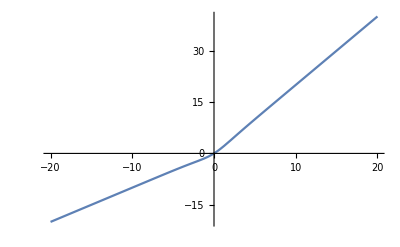

```mathematica
(* nonlinear, smooth approximation of a piecewise  linear objective function *)
p=1;
ftrue[x_]:=x(1+p(1+E^(-x))^(-1));
fmod[x_,a_,b_]:=x(1+b(1+E^(-a x))^(-1)); (*simplified form to have only two free parameters*)
Plot[ftrue[x],{x,-20,20}]
```

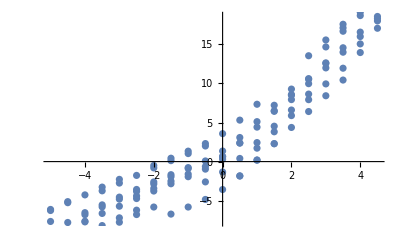

```mathematica
(* generate a sample from ftrue*)
nn=20;
ll=7;
xs = Table[xi-11,{ xi,1,nn}];
fi=Table[N[ftrue[x/.(x->xs[[i]])]],{i,1,Length[xs]}];
eps=4;
epss = RandomReal[{-eps,eps},ll*Length[fi]];
ys=Table[{xs[[i]],Table[fi[[i]]+epss[[i+j]],{j,0,ll-1}]},{i,1,Length[fi]}];
plots = Table[
ListPlot[Table[{0.5i-5.5,ys[[i,2]][[j]]},{i,1,nn}],PlotRange->All],{j,1,ll}];
Show[plots]
```

```mathematica
(* plot the loss, its gradient and hessian *)
loss[a_,b_]:=Sum[ Sum[(ys[[i,2]][[j]]-fmod[ys[[i,1]],a,b])^2,{j,1,ll}],{i,1,nn}];
Plot3D[loss[a,b],{a,-1.5,2},{b,-5,5},PlotRange->All, AxesOrigin->{0,0},
AxesLabel->{"a","b"}]
```

-Graphics3D-

```mathematica
(* check where the gradient is zero - in absolute value *)
absg[a_,b_]:=(Sqrt[D[loss[x,y],x]^2+D[loss[x,y],y]^2])/.{x->a,y->b}
zero[a_,b_]:=0;
Plot3D[{zero[a,b],absg[a,b]},{a,-0.5,2},{b,-1,2},PlotRange->All, AxesOrigin->{0,0},
AxesLabel->{"a","b"}]
(* notice the spurious minimum at a <0, b \simeq 0*)
```

-Graphics3D-

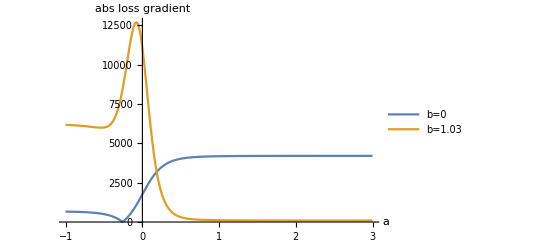

```mathematica
(* one dimensional projections of the abs gradient *)
Plot[{absg[a,0],absg[a,1.03]},{a,-1,3},PlotLegends->{"b=0","b=1.03"},
AxesLabel->{"a","abs loss gradient"}]
```

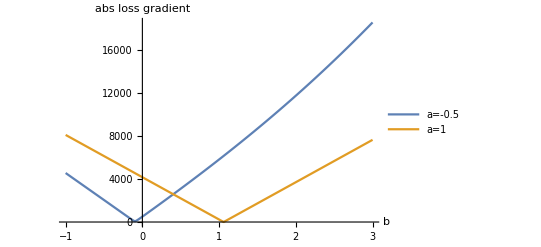

```mathematica
Plot[{absg[-0.5,b],absg[1,b]},{b,-1,3},PlotLegends->{"a=-0.5","a=1"},
AxesLabel->{"b","abs loss gradient"}]
```

```mathematica
(* notice the lower value of the hessian determinant (\simeq 0) at the true minimum - corresponding to higher stability of the loss w.r.t. small changes in the parameter b *)
```